now with constant focusing lens of target

plasma beam radius in mm

1.12505

focal length inwards

0.562525

focal length outwrds

-0.562525

0.568464-(1-1.7777 u) u

1.01056+(1-1.7777 u)^2

-0.568464-u (1+1.7777 u)

1.01056+(1+1.7777 u)^2

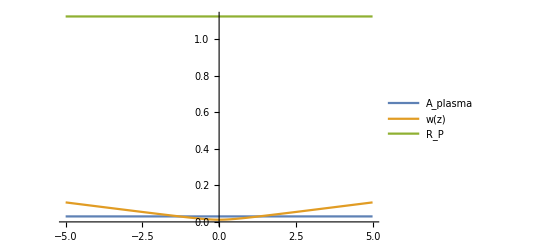

new focal position at

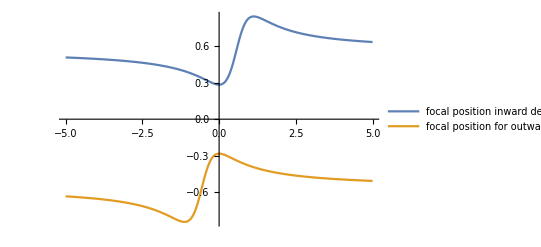

new beamwaist w0'

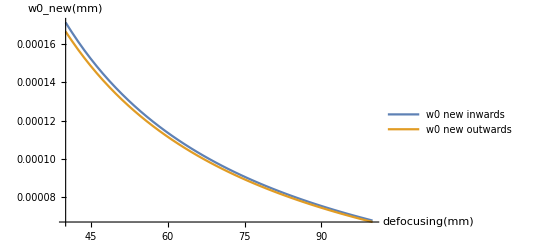

```mathematica
"now with constant focusing lens of target"

w0 = 0.012;
lambdaL = 0.0008;
D0 = 0.0001;
q = w0^2*π/(lambdaL);
"plasma beam radius in mm"
wzConst =0.03;
R = (4*(D0^2)+(wzConst^2))/(8*D0)
zr =  π*(w0^2)/lambdaL;
wz =  w0*(1+(u/zr)^2)^0.5;


"focal length inwards"
f1= R/2

"focal length outwrds"
fout= -R/2

AA = (((q^2)/f1) - u*(1-u/f1))
BB = ((q^2/f1^2)+(1-u/f1)^2)
A= (((q^2)/fout) - u*(1-u/fout))
B = ((q^2/fout^2)+(1-u/fout)^2)
vpositive = A/B;
vin= AA/BB;


Plot[{wzConst, wz, R},{u, -5,5}, PlotLegends->{"A_plasma", "w(z)", "R_P"}]


"new focal position at"
Plot[{vin, vpositive}, {u, -5,5}, PlotLegends->{"focal position inward denting", "focal position for outward denting"}, PlotRange->All]

wnew = √(w0^2*((1-vin/f1)^2+(1/q^2)*(u+vin*(1-(u/f1)))^2));

woutward = √(w0^2*((1-vpositive/fout)^2+(1/q^2)*(u+vpositive*(1-(u/fout)))^2));
"new beamwaist w0'"
Plot[{wnew, woutward}, {u, 40, 100}, PlotLegends->{"w0 new inwards ", "w0 new outwards"}, AxesLabel->{defocusing [mm], w0_new [mm]},PlotRange->All]

Clear[D0, R, zr, f1, fout, AA, BB, A, B, u, vpositive, vin, u, wnew, woutward]
```